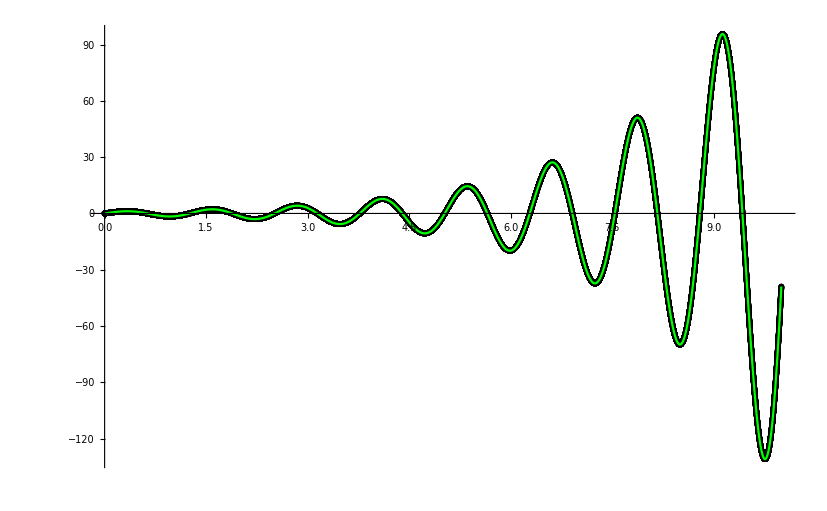

The Sum of Differences:

1.87668×10^-8

\begin{array}{ccc}
  & \text{x} & \text{Actual Error} \\
  & 0 & 0 \\
  & 1. & \text{3.426148253993233$\grave{ }$*${}^{\wedge}$-13} \\
  & 2. & \text{5.615508058554042$\grave{ }$*${}^{\wedge}$-13} \\
  & 3. & \text{1.4707346451814374$\grave{ }$*${}^{\wedge}$-11} \\
  & 4. & \text{3.243272317376977$\grave{ }$*${}^{\wedge}$-11} \\
  & 5. & \text{1.3546341826042863$\grave{ }$*${}^{\wedge}$-10} \\
  & 6. & \text{3.899138789620338$\grave{ }$*${}^{\wedge}$-10} \\
  & 7. & \text{9.512621801377463$\grave{ }$*${}^{\wedge}$-10} \\
  & 8. & \text{2.4257644781755516$\grave{ }$*${}^{\wedge}$-9} \\
  & 9. & \text{6.739071523043094$\grave{ }$*${}^{\wedge}$-9} \\
  & 10. & \text{1.889016942868693$\grave{ }$*${}^{\wedge}$-8} \\
\end{array}

```mathematica
SetDirectory["~/Desktop/School/College/Year 3/Foundations/Christmas Break Work/"];
data=Import["output.csv"];
(*f[t_,y_]:=-2y+2-E^(-4t)*)
f[t_,y_]:=y-1/2*E^(t/2)*Sin[5t]+5*E^(t/2)*Cos[5t]
sol[t_]=y[t]/.DSolve[{y'[t]==f[t,y[t]],y[0]==data⟦1⟧⟦2⟧},y[t],t]⟦1⟧⟦1⟧;
Show[ListPlot[data,PlotStyle->{Black,PointSize[.005]}],Plot[sol[t],{t,data⟦1⟧⟦1⟧,data⟦Length[data]⟧⟦1⟧},PlotStyle->Green,PlotRange->All],PlotRange->All,TicksStyle->Large]
TeXForm[TableForm[Table[{data⟦i⟧⟦1⟧,N[Abs[sol[data⟦i⟧⟦1⟧]-data⟦i⟧⟦2⟧],5]},{i,1,Length[data],Round[Length[data]/10]}],TableHeadings->{{},{"x","Actual Error"}}]]
Print["The Sum of Differences: "]
Sum[Abs[sol[data⟦i⟧⟦1⟧]-data⟦i⟧⟦2⟧]*Abs[data⟦i⟧⟦1⟧-data⟦i+1⟧⟦1⟧],{i,1,Length[data]-1}]
```

```mathematica
Length[data]
```

100001

```mathematica
sol[t]
```

ⅇ^(t/2) Sin[5 t]